## Binary classification of frozen input spike patterns by a somatic spike / no-spike code for the reward-modulated somato-dendritic synaptic plasticity (R-sdSP).

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Code

### Init

```mathematica
$HistoryLength=100;
```

#### compilation Attributes

```mathematica
Const/: (a_Symbol = Const[b_]) :=
(a =b; SetAttributes[a,Protected]; b)
```

```mathematica
SetAttributes[InlComp,HoldAll];
InlComp[inls_,parms_,code_,decl_] :=
Block[ {curprot,Trans2Rule,r1,r2,rcode,a,cmp,t},

curprot := Block[ {t,a,s} ,
t = Names[$Context<>"*"];
a = Map[Attributes,t];
t=t[[ Map[First,Position[a,Protected,{2}]] ]];t= Map[ToExpression[#,StandardForm,Hold]&,t]
];

SetAttributes[Trans2Rule,HoldAll];
    Trans2Rule[sym_] := Block[ {t},
t = DownValues[sym];
If [Length[t] == 0,
{HoldPattern[sym] -> sym},
t]
];

SetAttributes[cmp,HoldAll];

r1  = Apply[Trans2Rule,curprot,{1}];
r2 = Map[Trans2Rule,Unevaluated@inls];
rcode = Hold[code] //. Flatten[{r1,r2}];
t=cmp[parms,rcode,decl] /. HoldPattern[rcode]-> rcode /. Hold[a___] -> a;
Compile@@t
]
```

```mathematica
GlobalRefs[f_CompiledFunction]:= Block[ {a,b},
Cases[
f[[4]], 
HoldPattern[Function[a_List, b___]] -> HoldForm[b],
∞
]
]
```

## set values

```mathematica
NN=150;
 (* input dimension *)
Tmax = Const[500];  (* max. inputlength *)
step = 0.2; 
Tonl=Const[Tmax];(* τM in paper (for the elgibility trace low pass filter) *)
w = Table[1,{NN}]; (* no weight!!! *)
Urest = Const[-1] ;(* resting potential *)
(*α : factor of reduction of s^ν and Subscript[E, i] over one time step *)
α=N[1-step/Tonl];
(*β : factor of reduction of Subscript[e, i] over one time step *)
β=N[step/Tonl];
γ=N[1/Tonl];
(*invE : threshold for s^ν *)
tmr = 10.0; (* decay time of the reset kernel *)
tmrini =N[ 10/tmr]; (* constant to update resets of spiking neurons *)
tmrsfac=N[1-step/tmr]; (* factor of reduction of the reset kernel over one time step *)
rewdelay = 0.;(*delay for a reward *)
λ=1; (* smoothing factor for the exponential moving average *)
tNMDA=50//Const;(*duration of a NMDA spike *)
stNMDA= IntegerPart[tNMDA/step]; (* number of steps for a NMDA spike *)
stNMDAReal=1.0*stNMDA;(* number of steps for a NMDA spike *)
UspikeNMDA=0.3;
mu=0.1;
pConnect=0.5;(* connectivity probability *)
β2=5.;
Umax=10.0//Const (*for the dendritic branches*);
UmaxSoma=2.0//Const (*for the soma until le first order approx is quite correct*);
sigma=1.4;
pOff=0.2;
nbNeuron=40;
τfracSp=4;
msNumber=-Log[$MachineEpsilon *100.];
```

```mathematica
UrestSoma=Const[-1.];
```

```mathematica
cSpikeTime=Tonl/2;(* desired spike time *)
cSpikeTimeStep=cSpikeTime/step;(* desired spike time (number of step) *)
```

```mathematica
τfrac=0.5//Const (* fraction of time cte for the low pass filters *);
```

```mathematica
BoundSyn=100;
```

```mathematica
k2=Const[0.006737946999085467];
```

```mathematica
LearnSpike=True;
```

```mathematica
aAMPA:=N[1./(2*nbNeuron)];
```

```mathematica
stepperlist=0;(* to keep the membrane potential in "stepper" *)
```

```mathematica
setStep[newStep_]:=(step=newStep;αg=N[1-step/Tonl];βg=N[step/Tonl];γg=N[1/Tonl];αl=N[1-step/tNMDA];βl=N[step/tNMDA];γl=N[1/tNMDA];tmrsfac=N[1-step/tmr];stNMDA= IntegerPart[tNMDA/step];stNMDAReal=1.0*stNMDA;);
```

```mathematica
setStep[step];
```

## Develop functions

### load RandomBoolean

```mathematica
RandomBoolean[]:=If[RandomInteger[]==1,True,False];
```

### load packages

```mathematica
(* to write in the Messages windows *)
msg[expr_] := NotebookWrite[First@Notebooks["Messages"],
Cell[BoxData[MakeBoxes[expr,StandardForm]],"Output"]];
```

### define getFileName

```mathematica
getFileName[lstep_,trials_, opt_]:="./out/"<>"_eta"<>ToString[lstep//N]<>"_trials"<>ToString[trials]<>"_IL"<>ToString[NN]<>"_NbNeurons"<>ToString[nbNeuron]<>"_USpike"<>ToString[UspikeNMDA]<>"_Patn"<>ToString[Patn]<>"_SigmaW"<>ToString[σW]<>"_UrS"<>ToString[UrestSoma]<>"_aAMPA"<>ToString[aAMPA]<>"_"<>opt<>".out"
```

### define postsynaptic and reset kernel

```mathematica
myeps[] := Block[ {tm = 10.0,ts=1.5}, 
  (ⅇ^(-t/tm)-ⅇ^(-t/ts))/(tm-ts)]
```

```mathematica
myeta[]:= Block[ {tm = 10.0},
ⅇ^(-t/tm)/tm];
```

```mathematica
eps[t_] =myeps[];
SetAttributes[eps,Listable];
eta[t_] = 3myeta[];
SetAttributes[eta,Listable];
```

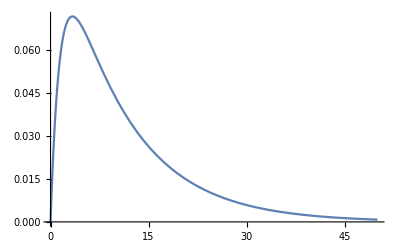

```mathematica
Plot[eps[t],{t,0,50}]
```

```mathematica
Integrate[eps[t],{t,0,∞}]
```

1.

### define stochastic intensity

```mathematica
(* escape noise for the dendrites *)
(*{ϕN,DϕN,DlϕN} = Block[ 
{k =100.(* firing at saturation *),β =5.0 (* Noise*),d =20000.0 (* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1+dd*Exp[-ββ*t]);
df =(kk*dd*ββ*Exp[-ββ*t])/(1+dd*Exp[-ββ*t])^2;
dlf = (ββ*dd)/(Exp[ββ*t]+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];*)
```

```mathematica
(* escape noise for the dendrites *)
{ϕN,DϕN,DlϕN} = Block[ 
{k =5.(* firing at saturation *),β =5.0 (* Noise*),d =1096.63 (* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1.0+dd*t);
df =(kk*dd*ββ*t)/(1.0+dd*t)^2;
dlf = (ββ*dd)/(1./t+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

```mathematica
(* escape noise for the soma *)
{ϕS,DϕS,DlϕS} = Block[ 
{k =k2,β =β2,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk ⅇ^(ββ *t);
df =kk ββ ⅇ^(ββ *t);
dlf = (*df/f*)ββ;
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

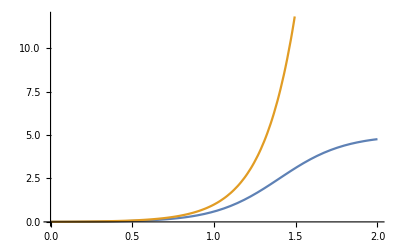

```mathematica
Plot[{ϕN[Exp[-β2 u]],ϕS[u]},{u,0,2}]
```

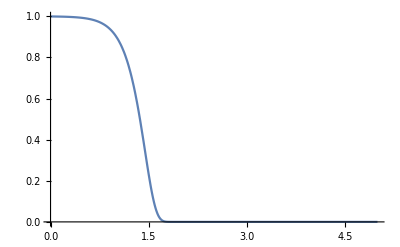

```mathematica
Plot[{step ϕS[u]/(ⅇ^(step ϕS[u])-1.)},{u,0,5},PlotRange->All]
```

```mathematica
step ϕS[u]/(ⅇ^(step ϕS[u])-1.)/.u->2
```

3.81504×10^-12

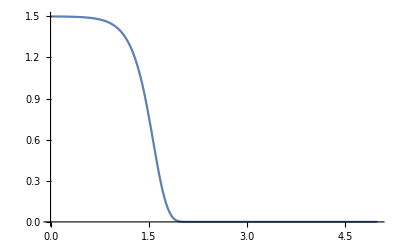

```mathematica
Plot[{Log[(1.-Exp[-ϕS[u]step])/(1.-Exp[- ϕS[u-0.3]step])]},{u,0,5},PlotRange->All]
```

```mathematica
1.-Exp[-ϕS[2.]step]
```

1.

```mathematica
Log[(1.-Exp[-ϕS[u]step])/(1.-Exp[- ϕS[u-0.3]step])]/.u->2.0
```

0.0013302

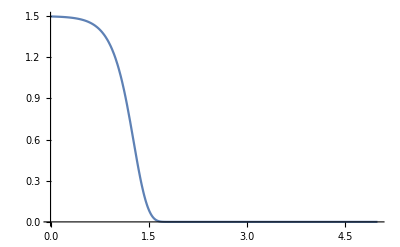

```mathematica
Plot[{Log[(1.-Exp[-ϕS[u+0.3]step])/(1.-Exp[- ϕS[u]step])]},{u,0,5},PlotRange->All]
```

```mathematica
Log[(1.-Exp[-ϕS[u+0.3]step])/(1.-Exp[- ϕS[u]step])]/.u->2.3
```

0.

### input: spikepattern X, corresponding synaptic potential epsps

```mathematica
Xin[]:=Block[{num=3,n,Xi},
    Xi:=(n=RandomInteger[PoissonDistribution[num]];
Sort[Table[RandomReal[] Tmax,{n}]]);
Table[Xi,{NN}]
];
```

```mathematica
Inp[t_,X_,func_] :=
 (* add up the various spikes defined by <func> *)
Apply[Plus,
 func[
(* delete the negative times *)
 DeleteCases [t-X, a_/; a <0 ,{-1}]] ,
{1}(* only at the first level*) ];
```

```mathematica
Itimes = Table[ i step, {i,0,Floor[Tmax/step]}];
```

```mathematica
epsps[X_] :=Map[Inp[#,X,eps]&,Itimes]; (* Lists of synaptic potentials into each neuron for each (discretized) time *)
```

### define mempots

```mathematica
(* to calculate the membrane potential in the dendritic branchs *)
mempots[w_,inp_] := Block[ {tmp,us},
us=w.Transpose[inp]+Urest;
(*us= us* UnitStep[Umax-us]+Umax*UnitStep[us-Umax];*)(*saturation of the membrane potential at Umax *)
us
];
```

### define spikegenNMDA

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_]:=
Block[{usf=Flatten[us],spikesi,t},
(*spikesi=Sign[step * ϕN[usf]-RandomReal[{0,1},Length[usf]]];*)
spikesi=Sign[1.-Exp[-step * ϕN[usf]]-RandomReal[{0,1},Length[usf]]];
If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_,refPeriod_]:=
Block[{usf=Flatten[us],spikesi,t},
spikesi=Sign[step * ϕN[usf]*refPeriod-RandomReal[{0,1},Length[usf]]];If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

### define myUnitStep

```mathematica
(Min[(tNMDA/(tNMDA+step)),Tonl/(Tonl+step)]+0.00001)/1000
```

0.000996026

```mathematica
myUnitStep[numb_]:=Block[{},
0.5*(Sign[(numb)+0.00099602593625498]+1.0)
];
```

### define ToFloat

```mathematica
ToFloat[numb_]:=Block[{numFl},
numFl=(numb*1.0);
numFl
];
```

### define SomaSat

```mathematica
SomaSat[u_]:=myUnitStep[UmaxSoma-u]u+myUnitStep[u-UmaxSoma]UmaxSoma;
```

### define stepper

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Urest,msNumber,UmaxSoma,SomaSat},
{{myinps,_Real,2},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Length[myinps];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

thisinp ={nmyinps[[i]]};   (* vector of inputs as a matrix *)
ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1,
EligSoma=(*dendStructSpUpd*)Log[(1.-Exp[-FRS ⅇ^(nUspikeNMDA β2  inRefPer)])/(1.-Exp[-FRS ⅇ^(-nUspikeNMDA β2 (1.-inRefPer))])];
Updinc=(naAMPA* DlϕS[uSoma*dendStruct]FRS/(ⅇ^FRS-1.)).thisinp;
nmyreset+=ntmrini;
Sow[ i];,

EligSoma=-(step*κ)*Exp[β2*SomaSat[(uSoma-nUspikeNMDA)+nUspikeNMDA*inRefPer]];
Updinc=(-naAMPA*step*DϕS[SomaSat@uSoma*dendStruct]).thisinp;
];

ntUpd =Updinc+0.5 ntAttIntNMDA*EligSoma*inRefPer+0.5 ntAttIntSpikeNMDA*EligSoma*(1.0-inRefPer)(**(0.5(Sign[NMDASpikeCounts-0.1] +1.) )*);(*temrm without attenuation *)

(* calc of the eligibilite trace *)
Updinc =(step*DϕN[argFI]).thisinp;


(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = argFI[[spikesNMDA]];
Updinc[[spikesNMDA]]=0.0*Updinc[[spikesNMDA]];
ntAttIntNMDA[[spikesNMDA]]=Updinc[[spikesNMDA]];
ntAttIntSpikeNMDA[[spikesNMDA]]=( DlϕN[us]).thisinp;

)];

(*myET=ntUpd+myET;*)
myET=ntUpd+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

(*ntAttIntNMDA=ntAttIntNMDA-nBufUpd[[indBuff]];
nBufUpd[[indBuff]]=Updinc;
ntAttIntNMDA=ntAttIntNMDA+Updinc;*)
ntAttIntNMDA=Updinc+(1.0-step/(τfrac*tNMDA))*ntAttIntNMDA;
(*ntAttIntSpikeNMDA=(1.0-step/(nτfracSp*tNMDA))*ntAttIntSpikeNMDA;*)
];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

```mathematica
GlobalRefs[stepper]
```

{}

### define passEpisode

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisode[w_, inps_] := passEpisode[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisode[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepper[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisode[inps_,lresl_] := (
passEpisode[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisode[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisode[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

### define iniws (initial weights and Mask)

```mathematica
iniws[w_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Norm[w,1]/Length[w];tmp=Table[w,{num}]+RandomReal[NormalDistribution[0,tmp],{num,Length[w]}];Mask=RandomReal[{0,1},{num,Length[w]}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### define myiniws

```mathematica
myiniws[μw_,σw_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Table[μw,{num},{NN}];If[σw≠0,tmp+=RandomReal[NormalDistribution[0,σw],{num,NN}]];
Mask=RandomReal[{0,1},{num,NN}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### Def. functions to create patterns

```mathematica
Patn=5;
 
(* number of patterns *)
Pats=Table[Xin[],{Patn}];
```

```mathematica
FlucLen=0;
MakePats[]:=(Pats=Table[Xin[],{Patn}];PatLen=Table[1+Round[(Tonl+2 FlucLen (Tmax-Tonl) (RandomReal[]-0.5))/step],{Patn}];)
```

```mathematica
Patsepsps0[n_] := Take[epsps[Pats[[n]]],PatLen[[n]]];
Clear[Patsepsps]; 
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(* patters as potentials *)
```

### define rewardFct

```mathematica
rewardFct[d_]:=-d/cSpikeTimeStep;
```

```mathematica
SetAttributes[rewardFct,Listable];
```

```mathematica
rewardFct2[d_]:=(Exp[-(d*step)^2/250^2]-1);
```

```mathematica
SetAttributes[rewardFct2,Listable];
```

```mathematica
(*give the Mean of the Initial Weights s.t. 80% of the synapses are exitatory*)
getMeanInitWeights[σ_,pOff_] := √2*σ*InverseErf[1-2.*pOff];
```

```mathematica
pOff=0.2;
```

### define learn

```mathematica
rewdelay=0.;
learnEpisodes[wwin_,trials_,lstep_]:=Block[{last,ensrew=0,ww,n,c,o,nw,thisstep,dw,dwl,wl,cutoff,ensgood,rewb,rews,resets,Z,Y,temp,t},
last=ini[wwin];
rewb=(R[#1,50+rewdelay,rewdelay,0.1]&)/@Itimes-1;
λ =0.2;
For[i=1,i≤trials,i++,
n=Ceiling[RandomReal[] Patn];(* choose ramndom pattern *)
{last,{Y,Z}}=nextpassEpisode[Patsepsps[n],last];
last=Last@last;(*we don't care about membrane pot*)
t=If[LearnSpike,If[n≤Round[Patn/2],0,1],If[n≤Round[Patn/2],1,0]];
ensgood=If[Sign@Length@Flatten@Z==t,1,0];

(*temp=o;*)
o=last[[4]]* Mask;

last[[1]]=last[[1]]+ lstep *(ensgood-1)*(last[[4]]* Mask);(* weight update *)
temp=UnitStep[BoundSyn-Abs[last[[1]]]];
last[[1]]=temp*last[[1]]+(1.-temp)*BoundSyn;(* only weights smaller BoundSyn *)

ensrew=(1-λ) ensrew+λ (ensgood);(* performance percentage as running mean *)(*If[Mod[i-1,10]==0,msg[{i,n,t,ensfield,o,Length[Patsepsps[n]]}]];*)
Sow[{ensgood,Length@Z,Map[Length,Y],Max@Abs@o(*Norm[o]*),Norm@First@last},ensemble];
(*msg[Z];*)
];
First@last
];
```

```mathematica
(*give the Mean of the Initial Weights s.t. 80% of the synapses are exitatory*)
getMeanInitWeights[σ_,pOff_] := √2*σ*InverseErf[1-2.*pOff];
```

### define learnInFile

```mathematica
learnInFile[trials1_,trials2_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,tmpSeed},
tmpSeed=IntegerPart[AbsoluteTime[]];
SeedRandom[tmpSeed];
Print["seed="<>ToString@tmpSeed];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
LearnSpike=RandomBoolean[];
(* patters as binarypotentials *)

tmp=Reap[learnEpisodes[wwin,trials1,lstep],ensemble];
res=trialDT[outDT[Transpose[tmp[[2,1]]][[1]](* Perf *)],
outDT[Transpose[tmp[[2,1]]][[2]](* Z *)],
outDT[0],
outDT[Transpose[tmp[[2,1]]][[4]](* |Δw| *)],
outDT[tmp[[1]](* w *)],
outDT[tmpSeed]];
PutAppend[res,(getFileName[lstep,trials1, opt])];
If[trials2>0,
tmp2=Reap[learnEpisodes[tmp[[1]],trials2,lstep],ensemble];
res=trialDT[outDT[Join[Transpose[tmp[[2,1]]][[1]],Transpose[tmp2[[2,1]]][[1]]](* Perf *)],
outDT[Join[Transpose[tmp[[2,1]]][[2]],Transpose[tmp2[[2,1]]][[2]]](* Z *)],
outDT[0],
outDT[Join[Transpose[tmp[[2,1]]][[4]],Transpose[tmp2[[2,1]]][[4]]](* |Δw| *)],
outDT[tmp2[[1]]],
outDT[tmpSeed]];
PutAppend[res,(getFileName[lstep,trials1+trials2, opt])];
];
];
```

### define ContlearnInFile

```mathematica
ContlearnInFile[trials1_,trials2_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,PerfTab,ZTab,YTab,ΔwTab},
res=ReadList[getFileName[lstep,trials1, opt]];

PerfTab=res/.trialDT[outDT[a_],_,_,_,_,_]->a;
ZTab=res/.trialDT[_,outDT[a_],_,_,_,_]->a;
YTab=res/.trialDT[_,_,outDT[a_],_,_,_]->a;
ΔwTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;

For[k=1,k≤Length@WTab,k++,
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
LearnSpike=RandomBoolean[];

Print@Timing[tmp2=Reap[learnEpisodes[WTab[[k]],trials2,lstep],ensemble];];
res=trialDT[outDT[Join[PerfTab[[k]],Transpose[tmp2[[2,1]]][[1]]](* Perf *)],
outDT[Join[ZTab[[k]],Transpose[tmp2[[2,1]]][[2]]](* Z *)],
outDT[(*Join[YTab[[k]],Transpose[tmp2[[2,1]]][[3]]](* Y *)*)0],
outDT[Join[ΔwTab[[k]],Transpose[tmp2[[2,1]]][[4]]](* |Δw| *)],
outDT[tmp2],
outDT[Seedtab[[k]]]];
PutAppend[res,(getFileName[lstep,trials1+trials2, opt])];
];
];
```

### λFilter

```mathematica
(*exp. moving average *)
 λFilter[incs_,λ_] := Block[ {fm},
fm[s_,inc_] := (1-λ)s + λ inc; 
FoldList[fm,0.5,incs]//Rest
];
```

## Plot functions

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["ErrorBarPlots`"]
```

### Def PlotHistdFromFile

```mathematica
(* plot the output spike trains in a matrix*)
PlotHistdFromFile[nbTrials_,LearnRates_,opt_]:=
Block[{res,tmp,mm,sd},
tmp=ReadList[getFileName[LearnRates,nbTrials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
tmp=Map[Take[step*#,-50]& ,tmp];
sd=StandardDeviation@Flatten@tmp;
mm=Mean@Flatten@tmp;
tmp=Flatten@Map[If[Length[#]==0,{0},#]&,tmp,{2}];
Histogram[tmp,(*Automatic*){2},"Probability",PlotRange->All,AxesLabel->{"t_s","P(t_s)"},
PlotLabel->Style[Framed["μ="<>ToString[mm]<>";    σ="<>ToString[sd]],16]]
];
```

### define PlotPerfInFile

```mathematica
PlotPerfInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[outDT[a_],_,_,_,_,_]->a;
ListLinePlot[ λFilter[Mean@res,0.2/Patn],FrameLabel->{"trials","R(Z)"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0.5,1}]
];
```

```mathematica
PlotPerfsInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[outDT[a_],_,_,_,_,_]->a;
ListAnimate@Table[ListLinePlot[ λFilter[res[[i]],0.1/Patn],FrameLabel->{"trials","R(Z)"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[i],
Frame->True,PlotRange->{0.5,1}],{i,Length@res}]
];
```

```mathematica
PlotPerfInFile[names_,legends_]:=Block[{tmp,res},
res=Table[
λFilter[Mean[ReadList[n]/.trialDT[outDT[a_],_,_,_,_,_]->a],0.1/Patn],
{n,names}];
ListLinePlot[ res,FrameLabel->{"trials","R(Z)"},
PlotLegend->legends,LegendPosition->{1,-0.2}, LegendShadow->None,
Frame->True,PlotRange->{0.5,1}]
];
```

### define PlotWeightsInFile

```mathematica
PlotWeightsInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,_,outDT[a_],_]->a;
res=Select[Flatten@res,(#≠0.0) &];
Histogram[res,Automatic(*{2}*),"Probability",PlotRange->All,AxesLabel->{"W","P(W)"},
PlotLabel->Style[Framed["μ="<>ToString[Mean@res]<>";    σ="<>ToString[StandardDeviation@res]],16]]
];
```

### define PlotWEvolInFile

```mathematica
PlotWEvolInFile[trials_,lstep_,opt_,lambda_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,outDT[a_],_,_]->a;

ListLinePlot[ λFilter[Mean@res,lambda],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn],
Frame->True,PlotRange->{0,1}]
];
```

```mathematica
PlotWEvolInFileList[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,outDT[a_],_,_]->a;
ListAnimate[Table[
ListLinePlot[ λFilter[res[[n]],1],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Run="<>ToString[n],
Frame->True,PlotRange->{0,1}]
,{n,1,Length@res}]]
];
```

### define PlotMeanSomSpikeInFile

```mathematica
PlotMeanSomSpikeInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
res=Map[Length,res,{2}];
ListLinePlot[ λFilter[Mean@res,0.2/Patn],PlotRange->All,FrameLabel->{"trials","<|Z|>"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0,1}]
];
```

### Def PlotSpikeActivity

```mathematica
(* plot the output spike trains in a matrix*)
PlotSpikeActivity[nbTrials_,LearnRates_,opt_]:=
Block[{tmp,resD,i,j,tmpLen},
resD=ReadList[getFileName[LearnRates,nbTrials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;

tmp=Table[0,{Length@First@resD},{Tonl/step+1}];
For[i=1,i≤1Length@resD,i++,
tmpLen=Length@(resD[[i]]);
For[j=1,j≤tmpLen,j++,
If[Length@resD[[i,j]]≠0,
tmp[[{tmpLen-j+1},resD[[i,j]]]]+=1;,
tmp[[{tmpLen-j+1},1]]+=1;];
];
];

MatrixPlot[tmp,DataRange->{{1,Tonl},{1,nbTrials}},AspectRatio->1,PlotLabel->"η="<>ToString[LearnRates]<>"  n="<>ToString[nbTrials],DataReversed->{True,False}]
];
```

### define PlotMeanBranchSpikeInFile

```mathematica
PlotMeanBranchSpikeInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,outDT[a_],_,_,_]->a;
res=Map[Length,res,{3}];
res=Map[Mean,res,{2}];
ListLinePlot[ λFilter[Mean@res,0.2/Patn],PlotRange->All,FrameLabel->{"trials","<|Y|>"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0,1}]
];
```

### define ToErrorList

```mathematica
ToErrorList[ls_,points_]:=Module[{mean,error},
mean=Prepend[Transpose[{Range[Min[Length/@ls]],(Mean@ls)[[Range[Min[Length/@ls]]]]}][[points]],{1,.5}];
error=Prepend[1/√(Length@ls)(StandardDeviation@ls)[[Range[Min[Length/@ls]]]][[points]],0];
MapThread[{#1,ErrorBar[#2]}&,{mean,error}]
]
```

## Changed Fct

### define getNbDSpikePerAPFromFile

```mathematica
GetNbNMDAForAP[Z_,Y_]:=Block[{tmp},
tmp=Map[Length@Cases[Map[Max,#-Y],x_/;(x>0&&x<stNMDA)] &,Z];
If[tmp=={},{},Mean@tmp]
]
```

```mathematica
getNbDSpikePerAPFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;
N@Mean@Flatten@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[σW,√σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
{last,{Y,Z}}=nextpassEpisode[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
GetNbNMDAForAP[Z,Y]
,{k,Length@Seedtab}]
];
```

### define PlotMeanNMDAContrFromFile

```mathematica
PlotMeanNMDAContrFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[σW,√σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
{last,{Y,Z}}=nextpassEpisode[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
stepperlist=0;
Transpose[Most@Most@last][[3;;4]]
,{k,Length@Seedtab}];
res={Mean@First@res,Mean[res[[2]]],StandardDeviation[res[[2]]],{{250,0},{250,-UrestSoma}}};
ListLinePlot[ res,FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@WTab],
Frame->True,PlotRange->All,DataRange->{0,Length@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@First@res],"μ_AMPA="<>ToString[Mean[res[[2]]]],"σ_AMPA="<>ToString[Mean[res[[3]]]]},LegendPosition->{1,-0.2}, LegendShadow->None]

];
```

### define GetFinalStatFromFile

```mathematica
myMean[data_]:=If[Length@data==0,{},Mean@data]
```

```mathematica
GetFinalStatFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[σW,√σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
tmp=Transpose@Table[
{last,{Y,Z}}=nextpassEpisode[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
Join[Transpose[Most@Most@last][[3;;4]],
{GetNbNMDAForAP[Z,Y],If[Length[Z]==0,{0},Z]}
]
,{nbSample}];
stepperlist=0;
{Mean[tmp[[1]]],Mean[tmp[[2]]],N@myMean@Flatten[tmp[[3]]],Flatten[tmp[[4]]]}
,{k,Length@Seedtab}];
tmp=Cases[Flatten[step*res[[4]]],Except[0]];
{Mean[Flatten[res[[3]]]],
Histogram[Flatten[res[[4]]]*step,(*Automatic*){2},"Probability",
PlotLabel->Framed[Style["μ="<>ToString[Mean[tmp]]<>";    σ="<>ToString[StandardDeviation[tmp]],16]],PlotRange->All,AxesLabel->{"t_s","P(t_s)"}],
ListLinePlot[ {Mean[res[[1]]],Mean[res[[2]]],{{250,0},{250,-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@WTab],
Frame->True,PlotRange->All,DataRange->{0,Length@First@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten@First@res],"μ_AMPA="<>ToString[Mean@Flatten[res[[2]]]]},LegendPosition->{1,-0.2}, LegendShadow->None],
ListAnimate[Table[
ListLinePlot[ {res[[1]][[k]],res[[2]][[k]],{{250,0},{250,-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Run="<>ToString[k],
Frame->True,PlotRange->All,DataRange->{0,Length@First@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten@First@res],"μ_AMPA="<>ToString[Mean@Flatten[res[[2]]]]},LegendPosition->{1,-0.2}, LegendShadow->None]
,{k,Length@First@res}],AnimationRunning->False]
}
];
```

```mathematica
GetFinalStatFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[σW,√σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
tmp=Transpose@Table[
{last,{Y,Z}}=nextpassEpisode[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
Join[Transpose[Most@Most@last][[3;;4]],
{GetNbNMDAForAP[Z,Y],If[Length[Z]==0,{0},Z]}
]
,{nbSample}];
stepperlist=0;
{Mean[tmp[[1]]],Mean[tmp[[2]]],N@myMean@Flatten[tmp[[3]]],Flatten[tmp[[4]]]}
,{k,Length@Seedtab}];
tmp=step*Cases[Flatten[res[[4]]],Except[0]];
{Mean[Flatten[res[[3]]]],
Histogram[Flatten[res[[4]]]*step,(*Automatic*){2},"Probability",
PlotLabel->Framed[Style["μ="<>ToString[Mean[tmp]]<>";    σ="<>ToString[StandardDeviation[tmp]],16]],PlotRange->All,AxesLabel->{"t_s","P(t_s)"}],
ListLinePlot[ {Mean[res[[1]]],Mean[res[[2]]],{{250,0},{250,-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@WTab],
Frame->True,PlotRange->All,DataRange->{0,Length@First@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten@First@res],"μ_AMPA="<>ToString[Mean@Flatten[res[[2]]]]},LegendPosition->{1,-0.2}, LegendShadow->None],
ListAnimate[Table[
ListLinePlot[ {res[[1]][[k]],res[[2]][[k]],{{250,0},{250,-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Run="<>ToString[k],
Frame->True,PlotRange->All,DataRange->{0,Length@First@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten@First@res],"μ_AMPA="<>ToString[Mean@Flatten[res[[2]]]]},LegendPosition->{1,-0.2}, LegendShadow->None]
,{k,Length@First@res}],AnimationRunning->False]
}
];
```

## Simulation

```mathematica
NN=100;
UspikeNMDA=0.4;
nbNeuron=20;
pConnect=0.5;
Patn=4;
aAMPA=Round[N[0.2/Sqrt[nbNeuron*pConnect]],0.00000001];
```

### R-sdSP

```mathematica
σW=4.1;
```

```mathematica
Table[Print@Timing@learnInFile[20000,0,11,"OnlineRuleAMPA_Class6Hz"],{20}];
```

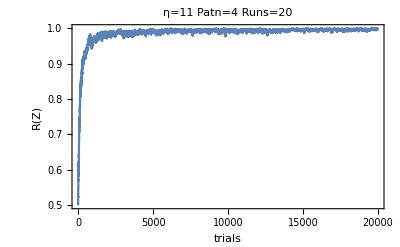

```mathematica
PlotPerfInFile[20000,11,"OnlineRuleAMPA_Class6Hz"]
```

```mathematica
getFileName[11,20000,"OnlineRuleAMPA_Class6Hz"]
```

./out/_eta11._trials20000_IL100_NbNeurons20_USpike0.4_Patn4_SigmaW4.1_UrS-1._aAMPA0.0632455_OnlineRuleAMPA_Class6Hz.out

### R-STDP(dendritic spikes-PSPs)

```mathematica
σW=4.2;
```

```mathematica
{Ap,An,τp,τn}={0.188,0(*-0.094/2*),10.,20.};
```

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,Urest,β2,tmrsfac,tmrini,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Ap,An,τp,τn},
{{myinps,_Real,2},   (* input potentials *)
{myinpsbin,_Real,2},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{APBuff,_Real,1}, (* mmemory of the AP *)
{PSPBuff,_Real,1} (* memory of the pre-synaptic spikes *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,inRefPer,nUspikeNMDA,κ,ntNMDASpBuff,EligSoma,ntPSPBuff,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,uTmp,DendStruct,nmyinps,nmyinpbins,naAMPA,nUrestSoma},

(*local compy to change of context only at the begining*)
nmyinps=myinps;
nmyinpbins=myinpsbin;
mask = Mask;
naAMPA=aAMPA;
nUrestSoma=UrestSoma;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Length[myinps];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
nmyresets =(*0.0**)resets (*Table[0,{Length@nw}]*);
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
DendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
ntNMDASpBuff=(*0.0**)APBuff(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = PSPBuff*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntPSPBuff=PSPBuff; 
ntUpd=0.0*nw;
uSoma=0.;
EligSoma=inRefPer;
uTmp=inRefPer;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

thisinp ={nmyinps[[i]]};   (* vector of inputs as a matrix *)
ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
spikesNMDA= spikegenNMDA[ud(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
NMDASpikeCounts=NMDASpikeCounts*(1.0-step/tNMDA);

SpikeSoma=0.5+0.5*Sign[1-Exp[-(step * ϕS[uSoma])]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1.0,
nmyreset+=tmrini;
Sow[ i];
];

ntNMDASpBuff=(1.0-step/τn)ntNMDASpBuff;
ntPSPBuff=Ap/τp*nmyinpbins[[i]]+(1.0-step/τp)ntPSPBuff;
ntUpd=0.ntUpd;
(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
ntUpd[[spikesNMDA ]]  =DendStruct[[spikesNMDA ]] .{ntPSPBuff};
ntNMDASpBuff[[spikesNMDA ]] +=An/τn;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = ud[[spikesNMDA]];
)];

ntUpd +=((DendStruct ntNMDASpBuff).{nmyinpbins[[i]]});
myET=ntUpd+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,ntNMDASpBuff,ntPSPBuff},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

```mathematica
Table[Print@Timing@learnInFile[20000,0,4.5,"OnlineNMDASTDPRule_tp10_Origin"],{20}];
```

$Aborted

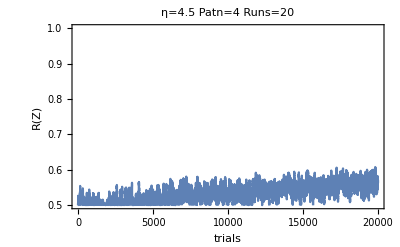

```mathematica
PlotPerfInFile[20000,4.5,"OnlineNMDASTDPRule_tp10_Origin"]
```

```mathematica
getFileName[4.5,20000,"OnlineNMDASTDPRule_tp10_Origin"]
```

./out/_eta4.5_trials20000_IL100_NbNeurons20_USpike0.4_Patn4_SigmaW4.2_UrS-1._aAMPA0.0632455_OnlineNMDASTDPRule_tp10_Origin.out

### R-STDP (APs-PSPs)

```mathematica
σW=4.2;
```

```mathematica
{Ap,An,τp,τn}={0.188,0(*-0.094/2*),10.,20.};
```

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,Urest,β2,tmrsfac,tmrini,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Ap,An,τp,τn},
{{myinps,_Real,2},   (* input potentials *)
{myinpsbin,_Real,2},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{APBuff,_Real}, (* mmemory of the AP *)
{PSPBuff,_Real,1} (* memory of the pre-synaptic spikes *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,inRefPer,nUspikeNMDA,κ,ntAPBuff,EligSoma,ntPSPBuff,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,uTmp,DendStruct,nmyinps,nmyinpbins,naAMPA,nUrestSoma},

(*local compy to change of context only at the begining*)
nmyinps=myinps;
nmyinpbins=myinpsbin;
mask = Mask;
naAMPA=aAMPA;
nUrestSoma=UrestSoma;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Length[myinps];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
nmyresets =(*0.0**)resets (*Table[0,{Length@nw}]*);
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
DendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
ntAPBuff=(*0.0**)APBuff(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = PSPBuff*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntPSPBuff=PSPBuff; 
ntUpd=0.0*ntPSPBuff;
uSoma=0.;
EligSoma=inRefPer;
uTmp=inRefPer;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

thisinp ={nmyinps[[i]]};   (* vector of inputs as a matrix *)
ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
spikesNMDA= spikegenNMDA[ud(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
NMDASpikeCounts=NMDASpikeCounts*(1.0-step/tNMDA);

SpikeSoma=0.5+0.5*Sign[1-Exp[-(step * ϕS[uSoma])]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1.0,
nmyreset+=tmrini;
Sow[ i];
];
ntAPBuff=An/τn SpikeSoma+(1.0-step/τn)ntAPBuff;
ntPSPBuff=Ap/τp*nmyinpbins[[i]]+(1.0-step/τp)ntPSPBuff;

ntUpd =(nmyinpbins[[i]]*ntAPBuff)+(SpikeSoma*ntPSPBuff);


(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = ud[[spikesNMDA]];
)];

myET=(DendStruct.{ntUpd})+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,ntAPBuff,ntPSPBuff},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

```mathematica
GlobalRefs[stepper]
```

```mathematica
Table[Print@Timing@learnInFile[20000,0,8.8,"OnlineSTDPRule_tp10_Origin"],{10}]
```

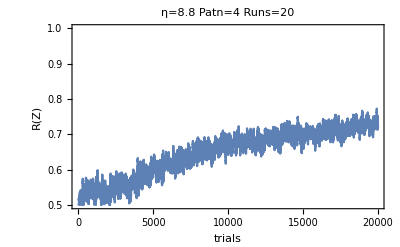

```mathematica
PlotPerfInFile[20000,8.8,"OnlineSTDPRule_tp10_Origin"]
```

```mathematica
getFileName[8.8,20000,"OnlineSTDPRule_tp10_Origin"]
```

### R-STDP (APs-PSPs but no NMDA spikes)

```mathematica
σW=18;
UspikeNMDA=0.0;
```

```mathematica
Table[Print@Timing@learnInFile[20000,0,35.3,"OnlineSTDPRule_tp10_Origin"],{10}];
```

$Aborted

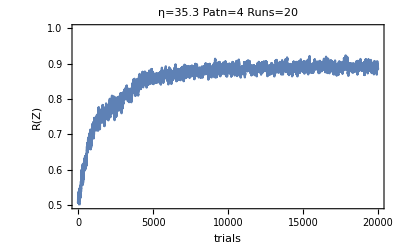

```mathematica
PlotPerfInFile[20000,35.3,"OnlineSTDPRule_tp10_Origin"]
```

```mathematica
getFileName[35.3,20000,"OnlineSTDPRule_tp10_Origin"]
```

./out/_eta35.3_trials20000_IL100_NbNeurons20_USpike0._Patn4_SigmaW18_UrS-1._aAMPA0.0632455_OnlineSTDPRule_tp10_Origin.out

## Comparisons

```mathematica
OptPadding={{42,26},{22,9}};
```

```mathematica
Patn=4;
```

```mathematica
STDPFileName="./out/_eta8.8_trials20000_IL100_NbNeurons20_USpike0.4_Patn4_SigmaW4.2_UrS-1._aAMPA0.0632455_OnlineSTDPRule_tp10_Origin.out";
```

```mathematica
PerfGlobSTDP=ReadList[STDPFileName]/.trialDT[outDT[a_],_,_,_,_,_]->a;
```

```mathematica
PerfGlobSTDP=Map[λFilter[#,0.2/Patn]&,PerfGlobSTDP];
```

```mathematica
PerfGlobSTDP=PerfGlobSTDP;
```

```mathematica
GlobRangeSTDP={1,1380}~Join~Range[2650,20000,2500]~Join~{20000};
ErrorPtsGlobSTDP=MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlobSTDP)[[GlobRangeSTDP]],(StandardDeviation@PerfGlobSTDP/Sqrt[Length@PerfGlobSTDP-1])[[GlobRangeSTDP]],GlobRangeSTDP}];
```

```mathematica
STDP2FileName="./out/_eta4.5_trials20000_IL100_NbNeurons20_USpike0.4_Patn4_SigmaW4.2_UrS-1._aAMPA0.0632455_OnlineNMDASTDPRule_tp10_Origin.out";
```

```mathematica
PerfGlobSTDP2=ReadList[STDP2FileName]/.trialDT[outDT[a_],_,_,_,_,_]->a;
```

```mathematica
PerfGlobSTDP2=Map[λFilter[#,0.2/Patn]&,PerfGlobSTDP2];
```

```mathematica
GlobRangeSTDP2={1,1130}~Join~Append[Range[2440,18000,2500],19850];
ErrorPtsGlobSTDP2=MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlobSTDP2)[[GlobRangeSTDP2]],(StandardDeviation@PerfGlobSTDP2/Sqrt[Length@PerfGlobSTDP2-1])[[GlobRangeSTDP2]],GlobRangeSTDP2}];
```

```mathematica
STDP3FileName="./out/_eta35.3_trials20000_IL100_NbNeurons20_USpike0._Patn4_SigmaW18_UrS-1._aAMPA0.0632455_OnlineSTDPRule_tp10_Origin.out";
```

```mathematica
PerfGlobSTDP3=ReadList[STDP3FileName]/.trialDT[outDT[a_],_,_,_,_,_]->a;
```

```mathematica
PerfGlobSTDP3=Map[λFilter[#,0.2/Patn]&,PerfGlobSTDP3];
```

```mathematica
GlobRangeSTDP3={1,1250}~Join~Append[Range[2500,20000,2520],20000];
ErrorPtsGlobSTDP3=MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlobSTDP3)[[GlobRangeSTDP3]],(StandardDeviation@PerfGlobSTDP3/Sqrt[Length@PerfGlobSTDP3-1])[[GlobRangeSTDP3]],GlobRangeSTDP3}];
```

```mathematica
rest=ReadList["./out/_eta11._trials20000_IL100_NbNeurons20_USpike0.4_Patn4_SigmaW4.1_UrS-1._aAMPA0.0632455_OnlineRuleAMPA_Class6Hz.out"];
```

```mathematica
PerfGlob=rest/.trialDT[outDT[a_],_,_,_,_,_]->a;
```

```mathematica
PerfGlob=Map[λFilter[#,0.2/Patn]&,PerfGlob];
```

```mathematica
GlobRange={1,1250}~Join~Append[Range[2500,20000,2520],20000];
ErrorPtsGlob=MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlob)[[GlobRange]],(StandardDeviation@PerfGlob/Sqrt[Length@PerfGlob-1])[[GlobRange]],GlobRange}];
```

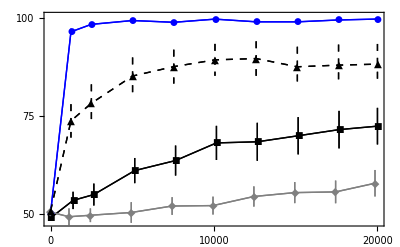

```mathematica
PlotPerfOnlinesbGR=Show[
ListLinePlot[{Transpose[{GlobRange,Mean[PerfGlob][[GlobRange]]}],Transpose[{GlobRangeSTDP,Mean[PerfGlobSTDP][[GlobRangeSTDP]]}],Transpose[{GlobRangeSTDP2,Mean[PerfGlobSTDP2][[GlobRangeSTDP2]]}],Transpose[{GlobRangeSTDP3,Mean[PerfGlobSTDP3][[GlobRangeSTDP3]]}]
},Joined->True,Frame->True,Axes->False,ImageSize->400,FrameTicks->{ {0,10000,20000},{ {0.5,50},{0.75,75},{1.0,100}}, None, None},BaseStyle->18,LabelStyle->(FontFamily->"Helvetica")(*,FrameLabel->{"trials","Performance (%)"}*),PlotRange->{0.48,1.005},PlotStyle->{{Blue,Thick},{Black,Thick},{Gray,Thick},{Black,Dashed,Thick}}(*,PlotMarkers->Automatic*)],
ErrorListPlot[{ErrorPtsGlob,ErrorPtsGlobSTDP,ErrorPtsGlobSTDP2,ErrorPtsGlobSTDP3},Joined->True,Frame->True,Axes->False,ImageSize->400,FrameTicks->{ {0,10000,20000},{ {0.5,50},{0.75,75},{1.0,100}}, None, None},BaseStyle->18,LabelStyle->(FontFamily->"Helvetica"),(*FrameLabel->{"trials","Performance (%)"},*)PlotRange->{0.45,1},PlotStyle->{{Blue,Thick},{Black,Thick},{Gray,Thick},{Black,Dashed,Thick}},PlotMarkers->Automatic],ImagePadding->OptPadding,ImageResolution->600]
```

```mathematica
Export["CompbSTDP-Online_4Patn-PSP.png",PlotPerfOnlinesbGR]
```

CompbSTDP-Online_4Patn-PSP.png